## Import Raw Data

```mathematica
rawCoordinates = Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx"];
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate;
```

```mathematica
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

## Split Ts

```mathematica
rawTs
```

{{,x},{1,1543466599},{2,1543466605},{3,1543466611},{4,1543466617},{5,1543466623},{6,1543466629},{7,1543466635},{8,1543466641},210335,{210344,1544821158},{210345,1544821164},{210346,1544821170},{210347,1544821176},{210348,1544821182},{210349,1544821188},{210350,1544821194},{210351,1544821200}}
 |  |  |  |

```mathematica
separatedTs=Rest[Split[rawTs[[All,2]],#2-#1<7&]];
```

```mathematica
{First[#],Last[#]}&/@separatedTs
```

{{1543466599,1543787095},{1543819592,1544129696},{1544160800,1544475116},{1544504034,1544821200}}

```mathematica
startEndHours=({First[#],Last[#]}&/@separatedTs-1543466599)/60/60//N;
```

```mathematica
startEndHours
```

{{0.,89.0267},{98.0536,184.194},{192.834,280.144},{288.176,376.278}}

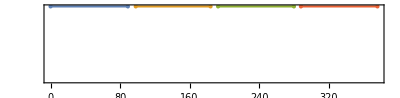

```mathematica
NumberLinePlot[Interval[#1]&/@startEndHours,Spacings->None,FrameTicks->{True,False},Frame->True, FrameLabel->Style["Hours since start of data collection",Medium],PlotLegends->LineLegend[MapIndexed[ToString[#2[[1]]]<>": "<>ToString[Round[#1[[2]]-#1[[1]]]]<>"h"&,startEndHours],LegendLabel->"Measurement Interval"]]
```

## Split rawCoordinates

```mathematica
splitSequences = Prepend[Accumulate[Length/@separatedTs],0];
```

```mathematica
splitRawCoordinates=BlockMap[rawCoordinates[[All,#[[1]]+1;;#[[2]]]]&,splitSequences,2,1];
```

```mathematica
splitRawCoordinates2=splitRawCoordinates/.Missing[]->Indeterminate;
```

```mathematica
Dimensions[splitRawCoordinates]
```

{4,51}

```mathematica
Dimensions/@splitRawCoordinates
```

{{51,53417,2},{51,51685,2},{51,52387,2},{51,52862,2}}

### Repeatability of mean for each time interval

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}];
```

```mathematica
Module[{currentPairData,data,splitCurrentPairData},
data=Table[
currentPairData=Import[FileNameJoin[{dataDirectory,name}]];
(*need to split first then delete missing data*)
splitCurrentPairData=DeleteCases[#,Indeterminate]&/@BlockMap[currentPairData[[#[[1]]+1;;#[[2]]]]&,splitSequences,2,1];
{Median/@splitCurrentPairData,Mean/@splitCurrentPairData},
{name,Flatten[PairNames]}];
medians=data[[All,1]];
means=data[[All,2]];]
Export[FileNameJoin[{dataDirectory,"groupedMedians.mx"}],medians];
Export[FileNameJoin[{dataDirectory,"groupedMeans.mx"}],means];
```

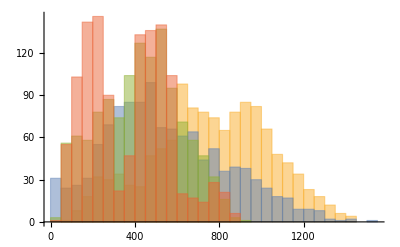

```mathematica
Histogram[DeleteCases[Transpose[means],Mean[{}],2]]
```

### Randomly picked distances

```mathematica
splitRandomDistances=Function[coord,Select[Table[EuclideanDistance@@coord[[RandomInteger[{1,Length[coord]},2],RandomInteger[{1,Length[coord[[1]]]}]]],10000],#>0&]]/@splitRawCoordinates2;
```